```mathematica
ClearAll["Global`*"]
d = 0.11;
v = 0.2;
vl[t] = v - (w[t] d)/2;
vr[t] = v + (w[t] d)/2;

plant = TransferFunctionModel[{{80/(1/2.5)v/s^2}},s] ;(* SISO *)
```

```mathematica
ctrl = PIDTune[plant, {"PID", Automatic}]
actrl = TransferFunctionModel[{{0.0988785+5/141 1/s + 0.0687s}}, s]
data = PIDTune[plant, {"PID", Automatic}, "PIDData"]
```

(0.0707 (0.5+1.06061 s+1. s^2))/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s110.0707$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

(0.0687 (0.516172+1.43928 s+1. s^2))/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s110.0687$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

PIDData[…]

```mathematica
sysol = SystemsModelSeriesConnect[actrl, plant]
syscl = SystemsModelFeedbackConnect[sysol, -1]
```

(2.748 (0.516172+1.43928 s+1. s^2))/s^3TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s112.7479999999999998$CellContext`s1FalseFalseFalseAutomaticNoneNoneAutomatic

(2.748 (0.516172+1.43928 s+1. s^2))/(s^3+3.95514 (0.358632+1. s+0.694792 s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s112.7479999999999998$CellContext`s1FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
respol = OutputResponse[sysol, UnitStep[t], {t,0,10}];
respcl = OutputResponse[syscl, UnitStep[t], {t,0,10}];
```

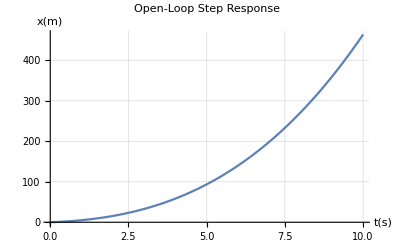

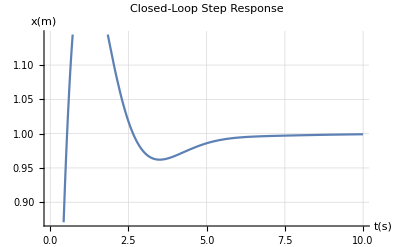

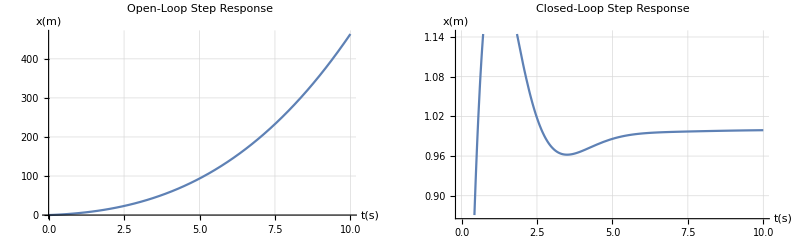

```mathematica
p1=Plot[respol, {t,0,10}, PlotLabel->"Open-Loop Step Response", GridLines->Automatic, AxesLabel->{t[s],x[m]}]
p2=Plot[respcl, {t,0,10}, PlotLabel->"Closed-Loop Step Response", GridLines->Automatic,
AxesLabel->{t[s],x[m]}]
g = GraphicsGrid[{{p1,p2}}]
```

```mathematica
Export["C:\\Users\\ycho\\Desktop\\Academics\\2017\\FA\\controls\\line_follower\\resp.eps",g,"EPS"]
```

C:\Users\ycho\Desktop\Academics\2017\FA\controls\line_follower\resp.eps

```mathematica
Simplify[(2.828(0.5+1.06s+s^2))/(s^3+2.9994(0.471428+s+0.942856 s^2))]
```

(2.828 (0.5+1.06 s+s^2))/(1.414+2.9994 s+2.828 s^2+s^3)